```mathematica
<< Toolbox`Style`
<< Toolbox`
SetDirectory[NotebookDirectory[]];
SetDirectory[".."];
<< util`
```

# SB2 Systems Biology : Simulation of Dynamic Network States

## Hemoglobin

### Construct model

```mathematica
hemoglobin=ExampleData[{"Toolbox","Hemoglobin"}];
```

```mathematica
hemoglobin["Parameters"]
```

{Volume_c→Liter,K_vdpgase→∞ Millimole Liter^-1,K_vdpgm→∞,K_vhbdpg→1/4 Liter Millimole^-1,K_vhbo1→41.8352 Liter Millimole^-1,K_vhbo2→73.2115 Liter Millimole^-1,K_vhbo3→177.799 Liter Millimole^-1,K_vhbo4→1289.92 Liter Millimole^-1,K_vo2→1,k_vdpgase^⟶→0.142258 Hour^-1,k_vdpgm^⟶→1814.81 Hour^-1,k_vhbo1^⟶→506935. Liter Hour^-1 Millimole^-1,k_vhbo2^⟶→511077. Liter Hour^-1 Millimole^-1,k_vhbo3^⟶→509243. Liter Hour^-1 Millimole^-1,k_vhbo4^⟶→501595. Liter Hour^-1 Millimole^-1,k_vhbdpg^⟶→519613. Liter Hour^-1 Millimole^-1,k_vo2^⟶→509726. Hour^-1,o2^Xt→0.0200788 Millimole Liter^-1}

```mathematica
rxns={Overscript[dpg23^c+h2o^c⇌pg3^c+phos^c, vdpgase],Overscript[pg13^c⇌dpg23^c+h^c, vdpgm],Overscript[dpg23^c+Hb^c⇌deoxyHb^c, vhbdpg],Overscript[o2^c+Hb^c⇌{{Hb^c, o2^c}}, vhbo1],Overscript[{{Hb^c, o2^c}}+o2^c⇌{{Hb^c, 2 o2^c}}, vhbo2],Overscript[{{Hb^c, 2 o2^c}}+o2^c⇌{{Hb^c, 3 o2^c}}, vhbo3],Overscript[{{Hb^c, 3 o2^c}}+o2^c⇌{{Hb^c, 4 o2^c}}, vhbo4],(o2^c⇌∅)^vo2};
```

```mathematica
conc={deoxyHb^c->0.04620957029335471 Millimole Liter^-1,Hb^c->0.059625251991425425 Millimole Liter^-1,{{Hb^c, o2^c}}->0.05008521167279736 Millimole Liter^-1,{{Hb^c, 2 o2^c}}->0.07362526115901212 Millimole Liter^-1,{{Hb^c, 3 o2^c}}->0.26284218233767326 Millimole Liter^-1,{{Hb^c, 4 o2^c}}->6.807612522545737 Millimole Liter^-1,o2^c->0.0200788 Millimole Liter^-1,dpg23^c->3.1 Millimole Liter^-1,pg13^c->0.000243 Millimole Liter^-1,pg3^c->0.0773 Millimole Liter^-1,phos^c->2.5 Millimole Liter^-1,h^c->0.00008997573444801929 Millimole Liter^-1,h2o^c->1. Millimole Liter^-1};
```

```mathematica
param={Underscript[Volume, c]->Liter,Underscript[K, vdpgase]->∞ Millimole Liter^-1,Underscript[K, vdpgm]->∞,Underscript[K, vhbdpg]->1/4 Liter Millimole^-1,Underscript[K, vhbo1]->41.835169432436196 Liter Millimole^-1,Underscript[K, vhbo2]->73.21154650676336 Liter Millimole^-1,Underscript[K, vhbo3]->177.79947008785382 Liter Millimole^-1,Underscript[K, vhbo4]->1289.9177241667828 Liter Millimole^-1,Underscript[K, vo2]->1,Subscript[k, vdpgase]^⟶->0.14225806451612902 Hour^-1,Subscript[k, vdpgm]^⟶->1814.8148148148148 Hour^-1,Subscript[k, vhbo1]^⟶->506935.270702259 Liter Hour^-1 Millimole^-1,Subscript[k, vhbo2]^⟶->511077.050923776 Liter Hour^-1 Millimole^-1,Subscript[k, vhbo3]^⟶->509243.459567699 Liter Hour^-1 Millimole^-1,Subscript[k, vhbo4]^⟶->501595.340624411 Liter Hour^-1 Millimole^-1,Subscript[k, vhbdpg]^⟶->519612.560391792 Liter Hour^-1 Millimole^-1,Subscript[k, vo2]^⟶->509725.707725914 Hour^-1,o2^Xt->0.0200788 Millimole Liter^-1};
```

```mathematica
hemoglobin=constructModel[rxns,InitialConditions->conc,Parameters->param,Ignore->{h2o^c,h^c},UnitChecking->True];
```

### Key ratios

```mathematica
keyRatios={"r_OHb"->100*({{Hb^c, o2^c}}+2 {{Hb^c, 2 o2^c}}+3 {{Hb^c, 3 o2^c}}+4 {{Hb^c, 4 o2^c}})/(4*(deoxyHb^c+Hb^c+3{{Hb^c, o2^c}}+2{{Hb^c, 2 o2^c}}+1{{Hb^c, 3 o2^c}}+{{Hb^c, 4 o2^c}}))};
```

### Analyze model

```mathematica
hemoglobinStandalone=hemoglobin;
updateBoundaryConditions[hemoglobinStandalone,{dpg23^c,pg13^c,pg3^c,phos^c,h2o^c,h^c}]
```

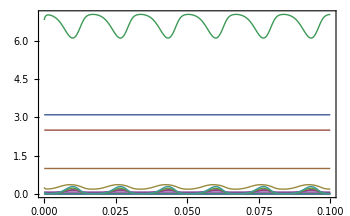

```mathematica
{concSol,fluxSol}=simulate[stripUnits@hemoglobinStandalone,{t,0,.1},Parameters->{m["o2","Xt"]->(30*Cos[120*Pi*t]+70)*0.00028684},MaxSteps->100000];
plotSimulation[concSol,PlotFunction->Plot,Tooltipped->False]
```

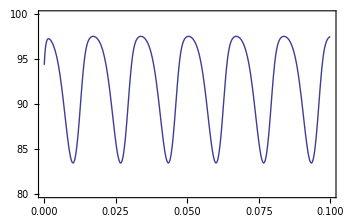

```mathematica
plotSimulation[keyRatios/.concSol,PlotFunction->Plot,PlotRange->{All,{80,100}}]
```

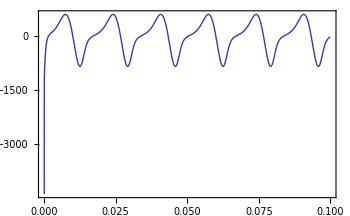

```mathematica
plotSimulation[filter[fluxSol,{v["vo2"]}],PlotFunction->Plot]
```

### Conversion factor

```mathematica
0.0031*40 *10*0.0554
0.0031*40 *100*0.0554
```

0.068696

0.68696

```mathematica
0.0031*40
```

0.124

```mathematica
0.0031*40(*mmHg*)*10(*to get liter*)
0.0031*100(*mmHg*)*10(*to get liter*)
```

1.24

3.1

```mathematica
N@ConvertTemperature[37 Celsius,Kelvin]
```

310.15 Kelvin

```mathematica
Convert[Mean[{0.04,0.12}]Millimole Liter^-1,Mole Liter^-1]
```

0.00008 Mole Liter^-1

```mathematica
SI[(1Atmosphere*1.24Milli Liter)/(MolarGasConstant*310.15 Kelvin)]
```

0.0487228 Millimole

```mathematica
SI[(1Atmosphere*3.1Milli Liter)/(MolarGasConstant*310.15 Kelvin)]
```

0.121807 Millimole

```mathematica
Convert[1.3*^-3Mole Liter^-1 Atmosphere^-1*Convert[40MillimeterMercury,Atmosphere],Millimole Liter^-1]
Convert[1.3*^-3Mole Liter^-1 Atmosphere^-1*Convert[100MillimeterMercury,Atmosphere],Millimole Liter^-1]
```

0.0684211 Millimole Liter^-1

0.171053 Millimole Liter^-1

```mathematica
Convert[0.136Mole Liter^-1,Millimole Liter^-1]
```

0.1768 Millimole Liter^-1

### Export

```mathematica
SetDirectory[NotebookDirectory[]];
Export["../../models/SB2/Hemoglobin.m.gz",hemoglobin]
```

../../models/SB2/Hemoglobin.m.gz